```mathematica
max6=Select[Keys[allGraphs6],MaximalPlanarQ[allGraphs6[#,"graph"]]&&VertexCount[allGraphs6[#,"graph"]]==6&]
```

{7174416,7174414,7174368,7174360,7174342,7174336,7174206,7174200,7174182,7174174,7174128,7174126,7173714,7173712,7173642,7173616,7173478,7173454,7172262,7172254,7172238,7172158,7172014,7171942,7171534,7171528,7171510,7171456,7167888,7167882,7167862,7167802,7167622,7167568,7167162,7167154,7167136,7166920,7165704,7165702,7165624,7165462,7154742,7154740,7154688,7154680,7154524,7154518,7154040,7154038,7153960,7153798,7152582,7152574,7152556,7152340,7148206,7148200,7148182,7148128,7115394,7115392,7115322,7115296,7115158,7115134,7113216,7112974,7112488,7108840,7108762,7108114,7095712,7095694,7094992,6997302,6997294,6997278,6997198,6997054,6996982,6996576,6996334,6994390,6990736,6990718,6988558,6977620,6977542,6975436,6938254,6938248,6938230,6938176,6937528,6936070,6643008,6643002,6642982,6642922,6642742,6642688,6642280,6642202,6640816,6640798,6635722,6634264,6623328,6623086,6616768,6583962,6583954,6583936,6583720,6583234,6577402,6465864,6465862,6465784,6465622,6463678,6459304,5580102,5580100,5580048,5580040,5579884,5579878,5579392,5579374,5577940,5577862,5573568,5573326,5559718,5558260,5553886,5521080,5521078,5521000,5520838,5520352,5501398,5402982,5402974,5402956,5402740,5400796,5383300,5048686,5048680,5048662,5048608,5042128,5029006,2391448,2391400,2391240,2390754,2390752,2390728,2389296,2389288,2389216,2384920,2384914,2384680,2371774,2371720,2371558,2332434,2332432,2332408,2330248,2325874,2312752,2214336,2214328,2214256,2213608,2207776,2194654,1860040,1860034,1859800,1859314,1857856,1840360,797134,797080,796918,796432,794974,790600}

```mathematica
FormulaSummary2[form_]:=Sort [Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[form]]]]
```

```mathematica
TableForm[Tally[Sort[Table[FormulaSummary2[allGraphs6[k,"colofour"]],{k,max6}]]],TableDepth->2]
```

{{3,1},{4,3},{5,1}} | 180
{{2,1},{3,3},{4,3},{5,1}} | 15

```mathematica
Select[max6,FormulaSummary2[allGraphs6[#,"colofour"]]=={{2,1},{3,3},{4,3},{5,1}}&]
```

{7112974,7108762,7095712,6996334,6990718,6977620,6642202,6640798,6623328,5579392,5577940,5573568,2391448,2391400,2391240}

```mathematica
FormulaSummary2[allGraphs6[7174416,"colofour"]]
```

{{3,1},{4,3},{5,1}}

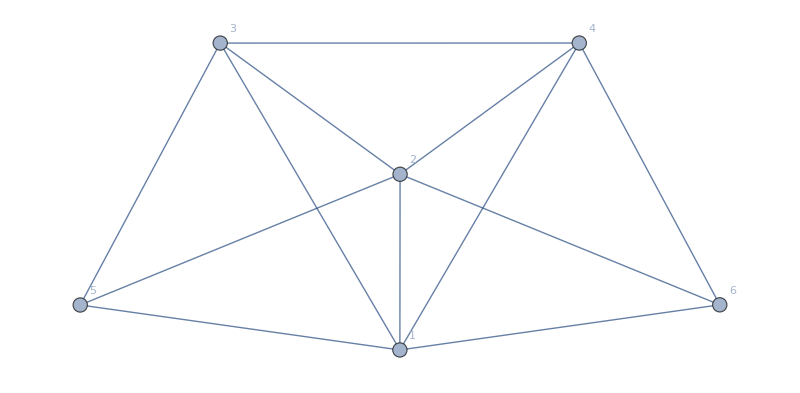

```mathematica
Graph[EdgeList[allGraphs6[7174416,"graph"]],VertexLabels->"Name", ImageSize->800]
```

```mathematica
FindClique[allGraphs6[7174416,"graph"],Infinity,All]
```

```mathematica
TableForm[Table[k->With[{g=Graph[plantri[[k]]]},
PrintTemporary["calculating",k];
With[{
form=FindFullFormula[g,Table[{j},{j,1,VertexCount[g]}]]},
Framed[
Column[
{
ChromaticPolynomial[g,4],
CompleteBaseCoeff[ ChromaticPolynomial[g,x]],
VertexCount[g],
Tally[Map[Length,FindClique[g,Infinity,All]]],
FormulaSummary2[form]
}
]
]
]
],{k,1,3}], TableDepth->2]
```

$Aborted

```mathematica
FindClique[allGraphs6[7112974,"graph"],Infinity,All]
```

{{4,5,6},{3,5,6},{2,4,6},{2,3,6},{1,4,5},{1,3,5},{1,2,4},{1,2,3}}

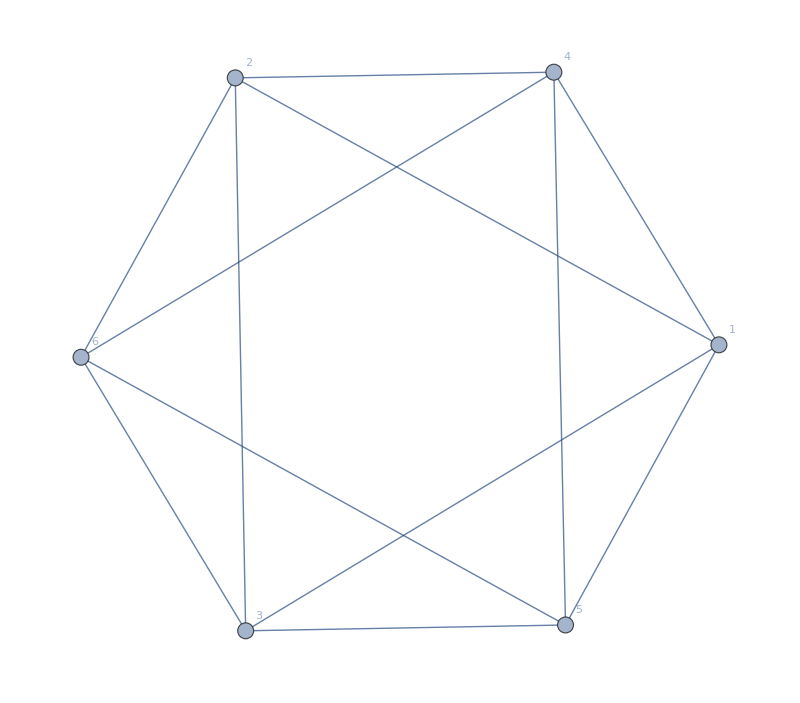

```mathematica
Graph[EdgeList[allGraphs6[7112974,"graph"]],VertexLabels->"Name", ImageSize->800]
```

```mathematica
Subsets[First[FindClique[Graph[plantri[[921]]],4]],{2}]
```

{{2,7},{2,8},{2,9},{7,8},{7,9},{8,9}}

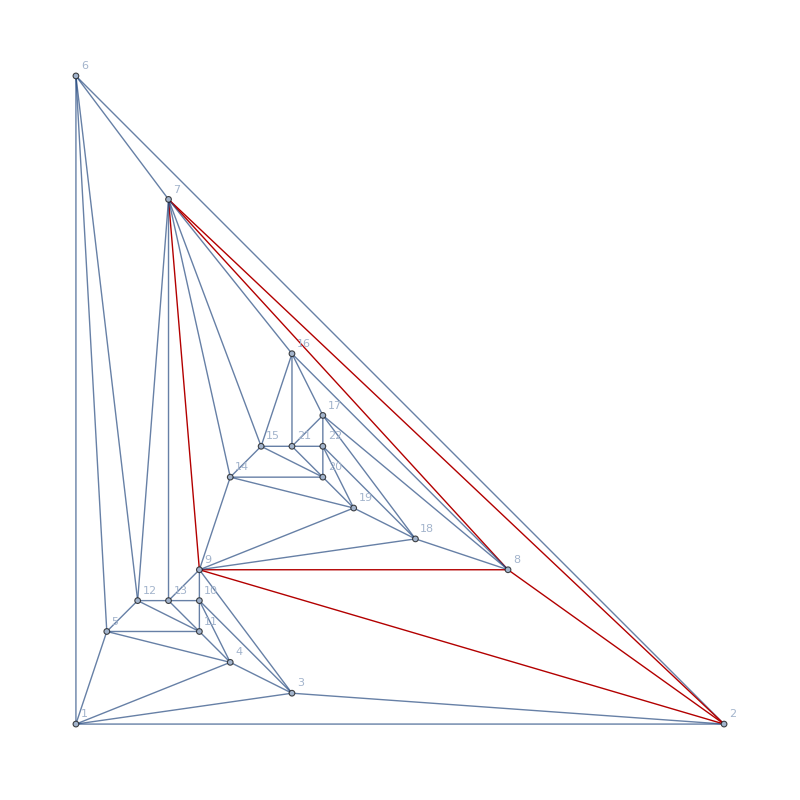

```mathematica
Graph[Graph[plantri[[921]]],VertexLabels->"Name", ImageSize->800,GraphHighlight->Map[#[[1]]<->#[[2]]&,Subsets[First[FindClique[Graph[plantri[[921]]],4]],{2}]], GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick"]
```